# Test Thruster Firing Mapping Algorithms

## General Setup

## 8 RCS Thruster Setup

```mathematica
setup8Thrusters:=Block[{},
rVec = {
{825.5/1000.0,880.3/1000.0,1765.3/1000.0},
{825.5/1000.0,880.3/1000.0,260.4/1000.0},
{880.3/1000.0,825.5/1000.0,1765.3/1000.0},
{880.3/1000.0,825.5/1000.0,260.4/1000.0},
{-825.5/1000.0,-880.3/1000.0,1765.3/1000.0},
{-825.5/1000.0,-880.3/1000.0,260.4/1000.0},
{-880.3/1000.0,-825.5/1000.0,1765.3/1000.0},
{-880.3/1000.0,-825.5/1000.0,260.4/1000.0}
};
COM = Mean[rVec];
gtVec = {
{0.0,-1.0,0.0},
{0.0,-1.0,0.0},
{-1.0,0.0,0.0},
{-1.0,0.0,0.0},
{0.0,1.0,0.0},
{0.0,1.0,0.0},
{1.0,0.0,0.0},
{1.0,0.0,0.0}
};
gtVecRed = Drop[gtVec,{1,8,2}];
rVecRed = Drop[rVec,{1,8,2}];

numThrusters = Length[rVec];
posThrustFlag =+1;
B = IdentityMatrix[3];
]

setup8Thrusters;
```

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVec[[i]],rVec[[i]]+.5gtVec[[i]]}]}
,{Black,PointSize[Large],Point[rVec[[i]]]}
}]
,{i,Length[rVec]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVecRed[[i]],rVecRed[[i]]+.5gtVecRed[[i]]}]}
,{Black,PointSize[Large],Point[rVecRed[[i]]]}
}]
,{i,Length[rVecRed]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

## 6 DV Thruster Setup

```mathematica
setup6DVThrusters:=Block[{},
gtVec = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVec = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];

rVecRed = Drop[rVec,{1}];
rVecRed = Drop[rVecRed,{3}];
gtVecRed = Drop[gtVec,{1}];
gtVecRed = Drop[gtVecRed,{3}];
numThrusters = Length[rVec];
posThrustFlag =-1;
B = {{1,0,0},{0,1,0}};
]
setup6DVThrusters;
```

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVec[[i]],rVec[[i]]+.5gtVec[[i]]}]}
,{Black,PointSize[Large],Point[rVec[[i]]]}
}]
,{i,Length[rVec]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVecRed[[i]],rVecRed[[i]]+.5gtVecRed[[i]]}]}
,{Black,PointSize[Large],Point[rVecRed[[i]]]}
}]
,{i,Length[rVecRed]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

## 8 RCS Thruster Setup (old config)

```mathematica
setup8ThrustersOldConfig:=Block[{},
rVec = {
{+1.125,0.0,+0.75},
{-1.125,0.0,+0.75},
{-1.125,0.0,+0.75},
{+1.125,0.0,+0.75},
{+1.125,0.0,-0.75},
{-1.125,0.0,-0.75},
{-1.125,0.0,-0.75},
{+1.125,0.0,-0.75}
};
COM=Chop[Mean[rVec]];
gtVec = {
{Sqrt[2.]/2,Sqrt[2.]/2,0},
{-Sqrt[2.]/2,Sqrt[2.]/2,0},
{-Sqrt[2.]/2,-Sqrt[2.]/2,0},
{Sqrt[2.]/2,-Sqrt[2.]/2,0},
{Sqrt[2.]/2,Sqrt[2.]/2,0},
{-Sqrt[2.]/2,Sqrt[2.]/2,0},
{-Sqrt[2.]/2,-Sqrt[2.]/2,0},
{Sqrt[2.]/2,-Sqrt[2.]/2,0}
};
gtVecRed = Drop[gtVec,{1,4}];
rVecRed = Drop[rVec,{1,4}];

numThrusters=Length[rVec];
posThrustFlag =+1;
B = IdentityMatrix[3];
]

setup8ThrustersOldConfig
```

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVec[[i]],rVec[[i]]+.5gtVec[[i]]}]}
,{Black,PointSize[Large],Point[rVec[[i]]]}
}]
,{i,Length[rVec]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVecRed[[i]],rVecRed[[i]]+.5gtVecRed[[i]]}]}
,{Black,PointSize[Large],Point[rVecRed[[i]]]}
}]
,{i,Length[rVecRed]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

## 12 RCS Thruster Setup

```mathematica
Lr = {1,2,3};
```

```mathematica
setup12Thrusters:=Block[{},
(* thruster locations *)
rVec = {
{1,0,0},
{1,0,0},
{-1,0,0},
{-1,0,0},
{0,1,0},
{0,1,0},
{0,-1,0},
{0,-1,0},
{0,0,1},
{0,0,1},
{0,0,-1},
{0,0,-1}
};
COM=Chop[Mean[rVec]];
gtVec = {
{0,1,0},
{0,-1,0},
{0,1,0},
{0,-1,0},
{0,0,1},
{0,0,-1},
{0,0,1},
{0,0,-1},
{1,0,0},
{-1,0,0},
{1,0,0},
{-1,0,0}
};
gtVecRed = Drop[gtVec,{1,12,2}];
rVecRed = Drop[rVec,{1,12,2}];

numThrusters=Length[rVec];
posThrustFlag = +1;
B = IdentityMatrix[3];
]

setup12Thrusters;
```

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVec[[i]],rVec[[i]]+.5gtVec[[i]]}]}
,{Black,PointSize[Large],Point[rVec[[i]]]}
}]
,{i,Length[rVec]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVecRed[[i]],rVecRed[[i]]+.5gtVecRed[[i]]}]}
,{Black,PointSize[Large],Point[rVecRed[[i]]]}
}]
,{i,Length[rVecRed]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

## Support Algorithm

```mathematica
monteCarloTest[rVec_,gtVec_] := MatrixForm[
Table[
evaluateForces[rVec,gtVec,{RandomReal[]-0.5,RandomReal[]-0.5,RandomReal[]-0.5},B,False]
,{i,10}]
]
```

```mathematica
thrPerformance[T_,F_,B_,gtVec_,Lr_]:= Chop[{
Norm[-Transpose[gtVec].F],
Norm[T.F - Transpose[B].B.Lr]/Norm[B.Lr]100,
Sum[F[[i]],{i,Length[F]}]
}]
```

```mathematica
barPlotStyle = {ChartLegends->functionNames
,ChartLabels->{Placed[caseNames,{{0.5,0.1},{0.8,1.2}},Rotate[#,0.5 Pi]&],Placed[{"",""},Above]}
,LabelingFunction->(Placed[Round[#1,0.01],Center]&)
,Axes->False
};
```

```mathematica
plotBarChart[data_,label_] := BarChart[data
,ChartLegends->functionNames
,ChartLabels->{Placed[caseNames,{{0.5,0.1},{0.8,1.2}},Rotate[#,0.5 Pi]&],Placed[{"",""},Above]}
,Axes->True
,BarSpacing->{0,1}
,PlotLabel->label
,ImageSize->{240,340}
,AxesOrigin->{0,0}
]
```

```mathematica
cost[T_,Lr_,B_,FF_]:=Block[{error,ans},

error=T.FF - Transpose[B].B.Lr ;

Return[error.error];
]
```

## Candidate Algorithms

## Simple Minimum Norm Torque solution on all Thrusters, make positive afterwards.

```mathematica
minNormTorque[rVec_, gtVec_,Lr_,B_,printFlag_]:=Block[{T,BT,F,F2},
F = Table[0,{i,Length[rVec]}];

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];
If[Det[T.Transpose[T]]>10^-6,
F2 = Transpose[T].Inverse[T.Transpose[T]].Transpose[B].B.Lr,
BT = B.T;
F2 =  Transpose[BT].Inverse[BT.Transpose[BT]].B.Lr;
];
(*F2 = PseudoInverse[T].Transpose[B].B.Lr;*)
If[printFlag,Print["F2(0):",F2]];
If[posThrustFlag>0,F2 -=Min[F2],F2 -= Max[F2]];
F = Chop[F2];
If[printFlag,Print["F2(1):",F2]];

If[printFlag,Print["Torque:",T.F]];

Return[thrPerformance[T,F,B,gtVec,Lr]];
]
evaluateForces = minNormTorque;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec];
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{0.807103,-0.994391,-1.80149,-0.807103,0.994391,1.80149}

F2(1):{-0.994391,-2.79589,-3.60299,-2.6086,-0.807103,0.}

Torque:{1.,2.,0.}

{10.809,0,5.40773}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.404955
0 | 0 | 0.233533
0 | 0 | 0.226627
0 | 0 | 0.245952
0 | 0 | 0.0930129
0 | 0 | 0.235691
0 | 0 | 0.370144
0 | 0 | 0.335774
0 | 0 | 0.157393
0 | 0 | 0.349524)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.171862,-0.824532,-0.110546,1.19479,-0.736678,-0.0840081,1.01909,-0.286254}

F2(1):{0.65267,0.,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Torque:{1.,2.,3.}

{0.392895,0,3.04273}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.0623021 | 0 | 0.476287
0.0652324 | 0 | 0.368581
0.0642857 | 0 | 0.384283
0.0968208 | 0 | 0.724397
0.0834423 | 0 | 0.653198
0.0925918 | 0 | 0.625228
0.0387823 | 0 | 0.228031
0.0305402 | 0 | 0.409075
0.0605164 | 0 | 0.341462
0.0426211 | 0 | 0.334684)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
numThrusters=8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.145781,-0.807281,-0.162708,1.16029,-0.762759,-0.10126,1.07125,-0.251751}

F2(1):{0.6615,0.,0.644572,1.96757,0.0445212,0.706021,1.87853,0.55553}

Torque:{1.,2.,3.}

{0.199105,0,3.01037}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.0426073 | 0 | 0.48218
0.0330219 | 0 | 0.383705
0.0429799 | 0 | 0.55216
0.017601 | 0 | 0.260779
0.0478324 | 0 | 0.613307
0.037282 | 0 | 0.412674
0.0265316 | 0 | 0.543175
0.0441189 | 0 | 0.51905
0.0211824 | 0 | 0.28101
0.0359435 | 0 | 0.553674)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### 0% COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
numThrusters=8;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.079977,-0.744473,-0.336361,1.16081,-0.744473,-0.079977,1.16081}

F2(1):{0.664496,0.,0.408112,1.90528,0.,0.664496,1.90528}

Torque:{1.,2.56018,2.38544}

{0.408112,22.2243,2.88269}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0.120694 | 30.0371 | 0.602801
0.178301 | 39.7751 | 0.567526
0.311567 | 38.4942 | 0.408914
0 | 46.5411 | 0.683926
0.0788357 | 28.1275 | 0.731997
0.477943 | 36.4268 | 0.592032
0 | 52.0757 | 1.19491
0.251491 | 44.4097 | 0.391763
0.373589 | 32.4165 | 0.451695
0.277675 | 29.9336 | 0.514648)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters=6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{0.807103,-0.994391,-1.80149,-0.807103,0.994391,1.80149}

F2(1):{2.6086,0.807103,0.,0.994391,2.79589,3.60299}

Torque:{1.,2.,0.}

{10.809,0,5.40773}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.04182 | 0 | 0.527642
1.67015 | 0 | 0.851126
1.61498 | 0 | 0.808935
1.79976 | 0 | 0.918047
1.39807 | 0 | 0.731896
0.555803 | 0 | 0.278526
1.6821 | 0 | 0.871477
2.40521 | 0 | 1.2676
1.81689 | 0 | 0.91017
1.99573 | 0 | 1.02131)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters=6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{0.849574,-0.950547,-1.7614,-0.772131,1.02799,1.83884}

F2(1):{2.61097,0.810853,0.,0.989268,2.78939,3.60024}

Torque:{0.788632,2.21137,0.}

{10.8007,13.3681,5.40331}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(2.20567 | 14.3594 | 1.10535
2.43015 | 14.4008 | 1.21782
0.781027 | 13.9556 | 0.390696
2.41198 | 13.9522 | 1.20626
1.66761 | 13.0437 | 0.849291
2.78108 | 13.8668 | 1.39119
1.29212 | 14.2797 | 0.648666
1.57398 | 14.287 | 0.787002
1.92281 | 12.8836 | 0.962228
2.59525 | 12.5824 | 1.3325)

### DV alignment, 0% COM, all thrusters, lost 2 thruster

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
rVecDV = Drop[rVecDV,{1}];
rVecDV = Drop[rVecDV,{3}];
gtVecDV = Drop[gtVecDV,{1}];
gtVecDV = Drop[gtVecDV,{3}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{-0.187289,-2.6086,0.187289,2.6086}

F2(1):{2.42131,0.,2.79589,5.21719}

Torque:{1.,2.,0.}

{10.4344,0,6.39522}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.28226 | 0 | 0.875531
2.84773 | 0 | 1.81615
1.42049 | 0 | 0.879927
2.63384 | 0 | 1.61317
1.12396 | 0 | 0.778538
2.85158 | 0 | 1.74646
1.18638 | 0 | 0.727128
2.65742 | 0 | 1.74686
1.58956 | 0 | 0.977308
1.27119 | 0 | 0.854149)

## 2-stage Min Torque solution subject to pos force on all Thrusters

```mathematica
minNormTorque2[rVec_, gtVec_,Lr_,B_,printFlag_]:=Block[{T,BT,F,F2, thrusterUsed,Dbar,i,c},
F = Table[0,{i,Length[rVec]}];

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

If[Det[T.Transpose[T]]>10^-6,
F2 = Transpose[T].Inverse[T.Transpose[T]].Transpose[B].B.Lr,
BT = B.T;
F2 =  Transpose[BT].Inverse[BT.Transpose[BT]].B.Lr;
];
(*F2 = PseudoInverse[T].Transpose[B].B.Lr;*)
If[printFlag,Print["F2(0):",F2]];

If[posThrustFlag>0,F2 -=Min[F2]];

If[printFlag,Print["F(2):",Chop[F2]]];
If[printFlag,Print["Rank:", MatrixRank[T]]];
If[printFlag,Print["T.F2:",T.F2]];


If[Length[rVec]==numThrusters && posThrustFlag==1,

F = F2,

thrusterUsed = Table[0,Length[rVec]];
Dbar = {};
Do[
If[F2[[i]]posThrustFlag>10^-8,
thrusterUsed[[i]] = 1;
AppendTo[Dbar,Cross[rVec[[i]]-COM,gtVec[[i]]]];
];
,{i,Length[rVec]}];
If[printFlag,Print["Dbar Length:", Length[Dbar]]];Dbar = Transpose[Dbar];
If[printFlag,Print["Dbar Rank: ", MatrixRank[Dbar]]];

If[Det[Dbar.Transpose[Dbar]]>10^-6,
F2 = Transpose[Dbar].Inverse[Dbar.Transpose[Dbar]].Transpose[B].B.Lr
,
BT = B.Dbar;
F2 =  Transpose[BT].Inverse[BT.Transpose[BT]].B.Lr;
];
(*F2 = PseudoInverse[Dbar].Transpose[B].B.Lr;*)
If[printFlag,Print["F2(2):",F2]];

c = 1;
F = Table[0,{i,Length[rVec]}];
Do[
If[thrusterUsed[[i]]>0,
F[[i]] = F2[[c]];
c += 1;
];
,{i,Length[rVec]}];
If[posThrustFlag>0,F -=Min[F]];
];


If[printFlag,Print["F:", N[F,14]]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
evaluateForces = minNormTorque2;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

Inverse::sing: Matrix {{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}} is singular.

F2(0):{{0.413,2.5289×10^-17,0.},{0.2065,-0.357668,0.},{-0.2065,-0.357668,0.},{-0.413,-7.58669×10^-17,0.},{-0.2065,0.357668,0.},{0.2065,0.357668,0.}}.Inverse[{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}].{1,2,3}

Inverse::sing: Matrix {{0.511707,0.,0.},{0.,0.511707,0.},{0.,0.,0.}} is singular.

F(2):{{0.413,0,0},{0.2065,-0.357668,0},{-0.2065,-0.357668,0},{-0.413,0,0},{-0.2065,0.357668,0},{0.2065,0.357668,0}}.Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}].{1,2,3}

Rank:2

T.F2:{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}.Inverse[{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}].{1,2,3}

F:{{0.413,2.5289×10^-17,0.},{0.2065,-0.357668,0.},{-0.2065,-0.357668,0.},{-0.413,-7.58669×10^-17,0.},{-0.2065,0.357668,0.},{0.2065,0.357668,0.}}.Inverse[{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}].{1.,2.,3.}

Torque:{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}.Inverse[{{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}}].{1,2,3}

Inverse::sing: Matrix {{0.511707,-1.249×10^-16,0.},{-1.249×10^-16,0.511707,0.},{0.,0.,0.}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{0.413,2.5289×10^-17,0.},{0.2065,-0.357668,0.},{-0.2065,-0.357668,0.},{-0.413,-7.58669×10^-17,0.},{-0.2065,0.357668,0.},{0.2065,0.357668,0.}}+Inverse[{«1»}]+{1,2,3} cannot be combined.

Thread::tdlen: Objects of unequal length in Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}]+{1,2,3}+{{0.413,0,0},{0.2065,-0.357668,0},{-0.2065,-0.357668,0},{-0.413,0,0},{-0.2065,0.357668,0},{0.2065,0.357668,0}} cannot be combined.

{Norm[-{{0,0,0},{0,0,0},{0,0,0}}.Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}].{1,2,3}],50 √(2/7) √(Abs[-3+{{0.511707,0,0},{0,0.511707,0},{0,0,0}}.Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}].{1,2,3}]^2+Abs[-2+{{0.511707,0,0},{0,0.511707,0},{0,0,0}}.Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}].{1,2,3}]^2+Abs[-1+{{0.511707,0,0},{0,0.511707,0},{0,0,0}}.Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}].{1,2,3}]^2),Inverse[{{0.511707,0,0},{0,0.511707,0},{0,0,0}}]+{1,2,3}+{{0.413,0,0},{0.2065,-0.357668,0},{-0.2065,-0.357668,0},{-0.413,0,0},{-0.2065,0.357668,0},{0.2065,0.357668,0}}}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 1.00237
0 | 0 | 1.26411
0 | 0 | 1.48113
0 | 0 | 1.54146
0 | 0 | 1.43253
0 | 0 | 1.80625
0 | 0 | 0.933476
0 | 0 | 1.45159
0 | 0 | 0.934757
0 | 0 | 1.56461)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.171862,-0.824532,-0.110546,1.19479,-0.736678,-0.0840081,1.01909,-0.286254}

F(2):{0.65267,0,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Rank:3

F:{0.65267,0,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Torque:{1.,2.,3.}

{0.392895,0,3.04273}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.102397 | 0 | 0.700683
0.0639473 | 0 | 0.416708
0.0892581 | 0 | 0.514634
0.0839221 | 0 | 0.540456
0.0610196 | 0 | 0.492511
0.0793207 | 0 | 0.679367
0.0383197 | 0 | 0.399166
0.0398455 | 0 | 0.325056
0.0768132 | 0 | 0.523779
0.0768318 | 0 | 0.43807)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.145781,-0.807281,-0.162708,1.16029,-0.762759,-0.10126,1.07125,-0.251751}

F(2):{0.6615,0,0.644572,1.96757,0.0445212,0.706021,1.87853,0.55553}

Rank:3

F:{0.6615,0,0.644572,1.96757,0.0445212,0.706021,1.87853,0.55553}

Torque:{1.,2.,3.}

{0.199105,0,3.01037}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.042308 | 0 | 0.478938
0.0123848 | 0 | 0.136221
0.044136 | 0 | 0.483578
0.0354222 | 0 | 0.398798
0.0296991 | 0 | 0.329814
0.0437814 | 0 | 0.800297
0.0495962 | 0 | 0.645124
0.0403382 | 0 | 0.473649
0.0234886 | 0 | 0.282056
0.0440732 | 0 | 0.60102)

### 0% COM, 1x rVec off by 1cm

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
gtVec2 = gtVec;
rVec2 =rVec;
rVec2[[1]] += {0,0.01,0};
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.171862,-0.824532,-0.110546,1.19479,-0.736678,-0.0840081,1.01909,-0.286254}

F(2):{0.65267,0,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Rank:3

T.F2:{1.,2.,3.}

F:{0.65267,0.,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Torque:{1.,2.,3.}

{0.392895,0,3.04273}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0.0690552 | 0 | 0.413068
0.0171562 | 0 | 0.336535
0.0655973 | 0 | 0.556366
0.0628228 | 0 | 0.357075
0.0815968 | 0 | 0.565542
0.0143043 | 0 | 0.224353
0.096504 | 0 | 0.585616
0.0352773 | 0 | 0.206766
0.0797315 | 0 | 0.506472
0.100429 | 0 | 0.726567)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### 0% COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
numThrusters = 8;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.079977,-0.744473,-0.336361,1.16081,-0.744473,-0.079977,1.16081}

F(2):{0.664496,0,0.408112,1.90528,0,0.664496,1.90528}

Rank:3

T.F2:{1.,2.56018,2.38544}

Dbar Length:5

Dbar Rank: 3

F2(2):{0.664496,1.15258,1.90528,0.664496,1.90528}

F:{0.664496,0,1.15258,1.90528,0,0.664496,1.90528}

Torque:{1.,2.,3.}

{1.15258,0,3.07763}

```mathematica
aaa=monteCarloTest[rVec2,gtVec2]
```

(0.00331144 | 0.613004 | 0.558231
0 | 0 | 0.306916
0.680516 | 0 | 0.76451
0.241225 | 0 | 0.576168
0.104722 | 0 | 0.423896
0.342141 | 0 | 0.378252
0.186249 | 0 | 0.227046
0.339329 | 0 | 0.49374
0.542187 | 0 | 0.724293
0 | 0 | 0.20074)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{0.807103,-0.994391,-1.80149,-0.807103,0.994391,1.80149}

F(2):{2.6086,0.807103,0,0.994391,2.79589,3.60299}

Rank:2

F:{2.6086,0.807103,0,0.994391,2.79589,3.60299}

Torque:{1.,2.,0.}

{10.809,0,5.40773}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(0.252926 | 0 | 0.131261
1.76444 | 0 | 0.88308
1.5309 | 0 | 0.789447
0.970657 | 0 | 0.508683
1.25182 | 0 | 0.630533
1.44676 | 0 | 0.723647
1.78917 | 0 | 0.941629
1.98359 | 0 | 1.01901
2.7256 | 0 | 1.40425
1.99428 | 0 | 0.997225)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{0.849574,-0.950547,-1.7614,-0.772131,1.02799,1.83884}

F(2):{2.61097,0.810853,0,0.989268,2.78939,3.60024}

Rank:2

F:{2.61097,0.810853,0,0.989268,2.78939,3.60024}

Torque:{0.788632,2.21137,0.}

{10.8007,13.3681,5.40331}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(2.21219 | 14.1294 | 1.11651
1.90861 | 11.6025 | 0.992671
2.00269 | 12.3422 | 1.04794
1.88436 | 14.1756 | 0.948209
1.47727 | 12.2129 | 0.746731
2.0251 | 11.9914 | 1.04242
2.39895 | 13.7966 | 1.20848
1.60082 | 12.5278 | 0.823024
1.85802 | 13.9383 | 0.930865
2.12976 | 14.395 | 1.0665)

### DV alignment, 0% COM, all thrusters, lost 2 thruster

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
rVecDV = Drop[rVecDV,{1}];
rVecDV = Drop[rVecDV,{3}];
gtVecDV = Drop[gtVecDV,{1}];
gtVecDV = Drop[gtVecDV,{3}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0):{-0.187289,-2.6086,0.187289,2.6086}

F(2):{2.42131,0,2.79589,5.21719}

Rank:2

Dbar Length:3

Dbar Rank: 2

F2(2):{-0.187289,0.187289,5.21719}

F(0):{-0.187289,0,0.187289,5.21719}

F:{0.,0.187289,0.374578,5.40448}

Torque:{1.,2.,0.}

{5.96635,0,5.42068}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.14443 | 0 | 0.922257
1.08944 | 0 | 0.836034
2.5754 | 0 | 2.00006
3.31239 | 0 | 2.10413
1.99093 | 0 | 1.25208
2.1371 | 0 | 1.77081
1.03416 | 0 | 0.892766
1.3776 | 0 | 0.88694
2.34177 | 0 | 1.62461
3.0062 | 0 | 1.99289)

## Pairing Solution

```mathematica
thrusterPairs[rVec_, gtVec_,Lr_,B_,printFlag_]:=Block[{T,F,F2,Tt,Tred},
F = Table[0,{i,Length[rVec]}];

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];
Tt=Transpose[T];
If[Length[rVec]==8,
Tred={
Tt[[1]]+Tt[[6]],
Tt[[2]]+Tt[[5]],
Tt[[3]]+Tt[[8]],
Tt[[4]]+Tt[[7]]
}];
If[Length[rVec]==7,
Tred={
Tt[[1]]+Tt[[6]],
Tt[[2]]+Tt[[5]],
Tt[[3]],
Tt[[4]]+Tt[[7]]
}];
If[Length[rVec]==4,
Tred= Tt;
];
If[Length[rVec]==6 || Length[rVec]==5,Return[{0,0,0}]];
Tred = Transpose[Tred];

F2 = PseudoInverse[Tred].Transpose[B].B.Lr;
If[printFlag,Print["F2(0):",F2]];
F2 -=Min[F2];
If[Length[rVec]==8,
F = Chop[{F2[[1]],F2[[2]],F2[[3]],F2[[4]],F2[[2]],F2[[1]],F2[[4]],F2[[3]]}]
];
If[Length[rVec]==7,
F = Chop[{F2[[1]],F2[[2]],F2[[3]],F2[[4]],F2[[2]],F2[[1]],F2[[4]]}]
];
If[Length[rVec]==4,
F = Chop[{F2[[1]],F2[[2]],F2[[3]],F2[[4]]}]
];
If[printFlag,Print["F2(1):",F2]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
];
evaluateForces = thrusterPairs;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
numThrusters=8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.122022,-0.786518,-0.210226,1.11877}

F2(1):{0.664496,0.,0.576292,1.90528}

Torque:{1.,2.,3.}

{0,0,2.96775}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.7145
0 | 0 | 0.530252
0 | 0 | 0.587591
0 | 0 | 0.63746
0 | 0 | 0.491747
0 | 0 | 0.293045
0 | 0 | 0.308323
0 | 0 | 0.593456
0 | 0 | 0.288972
0 | 0 | 0.254674)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.122022,-0.786518,-0.210226,1.11877}

F2(1):{0.664496,0.,0.576292,1.90528}

Torque:{1.,2.,3.}

{0,0,2.96775}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.282474
0 | 0 | 0.692088
0 | 0 | 0.31831
0 | 0 | 0.632576
0 | 0 | 0.591006
0 | 0 | 0.436837
0 | 0 | 0.500761
0 | 0 | 0.432782
0 | 0 | 0.120382
0 | 0 | 0.581958)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
numThrusters=8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0):{-0.122022,-0.786518,-0.210226,1.11877}

F2(1):{0.664496,0.,0.576292,1.90528}

Torque:{1.,2.,3.}

{0,0,2.96775}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.454572
0 | 0 | 0.43206
0 | 0 | 0.453446
0 | 0 | 0.338159
0 | 0 | 0.278522
0 | 0 | 0.477946
0 | 0 | 0.659091
0 | 0 | 0.553666
0 | 0 | 0.725378
0 | 0 | 0.310949)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### correct COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
numThrusters=8;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.0319254,-0.696421,-0.240258,1.20886}

F2(1):{0.664496,0.,0.456163,1.90528}

Torque:{1.,2.52402,2.4251}

{0.456163,20.7898,2.88988}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0 | 38.9653 | 0.571496
0.321056 | 46.9261 | 0.505621
0 | 31.9111 | 0.539685
0.378893 | 44.8716 | 0.516551
0.304747 | 29.3796 | 0.305575
0.192266 | 33.0804 | 0.344679
0 | 26.1434 | 0.6351
0.117738 | 34.1821 | 0.464598
0.272168 | 39.5135 | 0.711347
0.0306598 | 21.7696 | 0.445301)

## Min Torque solution Per Axis subject to pos force on all Thrusters

```mathematica
minNormTorquePerAxis[rVec_, gtVec_,Lr_,B_,printFlag_]:=Block[{T,BT,F,F2, thrusterUsed,DD,b,dum},
F = Table[0,{i,Length[rVec]}];

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

Do[
DD = {};
b = B[[j]];
Do[
AppendTo[DD,Cross[rVec[[i]]-COM,gtVec[[i]]].b];
,{i,Length[rVec]}];
dum = DD.DD;
If[dum>0.00001, dum = 1./dum, dum = 0];
F2=(DD dum) (Lr.b);
If[posThrustFlag>0,F2 -=Min[F2],F2 -= Max[F2]];
F += F2;

,{j,Length[B]}];
If[posThrustFlag>0,F -=Min[F],F -= Max[F]];

If[printFlag,Print["F:", F]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
evaluateForces = minNormTorquePerAxis;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{-0.994391,-2.79589,-3.60299,-2.6086,-0.807103,0.}

Torque:{1.,2.,0.}

{10.809,0,5.40773}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.39036
0 | 0 | 0.569219
0 | 0 | 0.236914
0 | 0 | 0.760181
0 | 0 | 0.326616
0 | 0 | 0.573872
0 | 0 | 0.665395
0 | 0 | 0.50439
0 | 0 | 0.20887
0 | 0 | 0.341121)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.65267,0.,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Torque:{1.,2.,3.}

{0.392895,0,3.04273}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.111502 | 0 | 0.6537
0.0903071 | 0 | 0.537683
0.0339006 | 0 | 0.229875
0.025536 | 0 | 0.154714
0.0744016 | 0 | 0.433751
0.021605 | 0 | 0.325685
0.100992 | 0 | 0.570787
0.0421431 | 0 | 0.354789
0.066079 | 0 | 0.553825
0.0535777 | 0 | 0.439052)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.6615,0.,0.644572,1.96757,0.0445212,0.706021,1.87853,0.55553}

Torque:{1.,2.,3.}

{0.199105,0,3.01037}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.0126505 | 0 | 0.164134
0.0222074 | 0 | 0.431644
0.021938 | 0 | 0.452255
0.0450713 | 0 | 0.572161
0.0242994 | 0 | 0.359385
0.0446965 | 0 | 0.493088
0.0131457 | 0 | 0.324045
0.0321424 | 0 | 0.509254
0.0234725 | 0 | 0.437189
0.0375021 | 0 | 0.510198)

### 0% COM, 1x rVec off by 1cm

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
gtVec2 = gtVec;
rVec2 =rVec;
rVec2[[1]] += {0,0.01,0};
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F:{0.65267,0.,0.713986,2.01933,0.0878539,0.740524,1.84362,0.538278}

Torque:{1.,2.,3.}

{0.392895,0,3.04273}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0.0894534 | 0 | 0.628073
0.0896093 | 0 | 0.507404
0.063847 | 0 | 0.660784
0.072957 | 0 | 0.418407
0.047163 | 0 | 0.385785
0.0687551 | 0 | 0.541831
0.0267374 | 0 | 0.316597
0.0246382 | 0 | 0.323067
0.0604767 | 0 | 0.353484
0.0988771 | 0 | 0.610712)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### 0% COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
numThrusters = 8;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F:{0.664496,0.,0.484585,2.25657,0.,0.664496,2.25657}

Torque:{1.,3.03129,3.02855}

{0.484585,27.573,3.36187}

```mathematica
aaa=monteCarloTest[rVec2,gtVec2]
```

(0.247013 | 50.6146 | 0.46277
0.0836175 | 30.194 | 0.495645
0.225091 | 46.4159 | 0.563455
0 | 23.7746 | 0.406145
0.158142 | 55.0645 | 0.292912
0 | 33.2132 | 0.582599
0.267533 | 80.0069 | 0.40189
0.213218 | 46.6222 | 0.555948
0.087468 | 29.4321 | 0.560035
0 | 27.4792 | 0.75899)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{2.6086,0.807103,0.,0.994391,2.79589,3.60299}

Torque:{1.,2.,0.}

{10.809,0,5.40773}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.38629 | 0 | 0.702396
2.53669 | 0 | 1.27245
1.85567 | 0 | 0.95694
2.37695 | 0 | 1.24068
2.21974 | 0 | 1.12676
0.839226 | 0 | 0.424231
0.930499 | 0 | 0.470106
0.634281 | 0 | 0.321183
2.8268 | 0 | 1.41683
1.78637 | 0 | 0.893365)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{2.59642,0.803335,0.,0.989749,2.78283,3.58617}

Torque:{0.780162,2.20583,0.}

{10.7585,13.4682,5.38248}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.69667 | 13.4146 | 0.858259
1.40863 | 13.7025 | 0.71143
0.917931 | 12.1675 | 0.480316
1.33622 | 13.4427 | 0.6755
1.44281 | 12.8083 | 0.747259
0.965664 | 13.2809 | 0.482976
2.87161 | 12.995 | 1.44201
0.443627 | 11.5359 | 0.233402
3.01889 | 13.0527 | 1.53321
1.75595 | 12.0748 | 0.920871)

### DV alignment, 0% COM, all thrusters, lost 2 thruster

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
rVecDV = Drop[rVecDV,{1}];
rVecDV = Drop[rVecDV,{3}];
gtVecDV = Drop[gtVecDV,{1}];
gtVecDV = Drop[gtVecDV,{3}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{2.42131,0.,2.79589,5.21719}

Torque:{1.,2.,0.}

{10.4344,0,6.39522}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(2.86759 | 0 | 1.82857
0.75944 | 0 | 0.504134
1.31389 | 0 | 0.816593
1.74477 | 0 | 1.07112
1.97297 | 0 | 1.21203
2.91825 | 0 | 1.7902
1.19026 | 0 | 0.729418
1.14219 | 0 | 0.710224
2.71966 | 0 | 1.67893
2.45841 | 0 | 1.54374)

## 2-stage Min Torque solution Per Axis subject to pos force on all Thrusters

```mathematica
minNormTorque2PerAxis[rVec_, gtVec_,Lr_,B_,printFlag_]:=Block[{T,BT,F,F2, thrusterUsed,DD,Dbar,b,dum,Dbar1,Dbar2,c},
F = Table[0,{i,Length[rVec]}];

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

Do[
DD = {};
b = B[[j]];
Do[
AppendTo[DD,Cross[rVec[[i]]-COM,gtVec[[i]]].b];
,{i,Length[rVec]}];
dum = DD.DD;
If[dum>0.00001, dum = 1./dum, dum = 0];
F2=(DD dum) (Lr.b);
If[posThrustFlag>0,F2 -=Min[F2],F2 -= Max[F2]];
If[printFlag,Print["F2(0)",F2]];
If[printFlag,Print["D:",DD]];

thrusterUsed = Table[0,Length[rVec]];
Dbar = {};
Do[
If[F2[[i]]posThrustFlag>10^-6,
thrusterUsed[[i]] = 1;
AppendTo[Dbar,Cross[rVec[[i]]-COM,gtVec[[i]]]];
];
,{i,Length[rVec]}];

If[printFlag,Print["Dbar Rank: ", MatrixRank[Transpose[Dbar]]]];
If[printFlag,Print["Length:", Length[Dbar]]];

If[Det[Transpose[Dbar].Dbar]>10^-6,
(* Minimum Norm Inverse *)
F2 = Dbar.Inverse[Transpose[Dbar].Dbar].(b Lr.b);
If[printFlag,Print["Dbar.F:",Transpose[Dbar].F2]];
If[printFlag,Print["F2:",F2]];
,
(* Least Square Inverse *)
(*If[Det[Dbar.Transpose[Dbar]]>0.00001,*)
BT = b.Transpose[Dbar];
F2 = BT/(BT.BT)*( Lr.b);

];
If[printFlag,Print["F2:",F2]];
If[printFlag,Print[thrusterUsed]];

c = 1;
Do[
If[thrusterUsed[[i]]>0,
F[[i]] += F2[[c]];
c += 1;
];
,{i,Length[rVec]}];
(*Print["F:", F];
Print["DD.F:",DD.F];*)

,{j,Length[B]}];
If[posThrustFlag>0,F -=Min[F],F -= Max[F]];

If[printFlag,Print["F:", F]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
evaluateForces = minNormTorque2PerAxis;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0){0.,-0.403551,-1.21065,-1.61421,-1.21065,-0.403551}

D:{0.413,0.2065,-0.2065,-0.413,-0.2065,0.2065}

Dbar Rank: 2

Length:5

F2:{0.605327,-0.605327,-1.21065,-0.605327,0.605327}

{0,1,1,1,1,1}

F2(0){-1.39794,-2.79589,-2.79589,-1.39794,-6.66134×10^-16,0.}

D:{5.30445×10^-17,-0.357668,-0.357668,-4.81113×10^-17,0.357668,0.357668}

Dbar Rank: 2

Length:4

F2:{4.14648×10^-16,-2.79589,-2.79589,-3.76085×10^-16}

{1,1,1,1,0,0}

F:{-0.605327,-2.79589,-4.00654,-1.81598,-1.21065,0.}

Torque:{1.,2.,0.}

{10.4344,0,5.38509}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0 | 0 | 0.436368
0 | 0 | 0.348786
0 | 0 | 0.625336
0 | 0 | 0.273589
0 | 0 | 0.388383
0 | 0 | 0.0840562
0 | 0 | 0.534264
0 | 0 | 0.376282
0 | 0 | 0.389532
0 | 0 | 0.348067)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0){0.65267,0.,0.370262,0.370262,0.0878539,0.740524,0.370262,0.370262}

D:{0.651165,-0.853735,0.,0.,-0.651165,0.853735,0.,0.}

Dbar Rank: 3

Length:7

Dbar.F:{1.,0.,-8.32667×10^-17}

F2:{0.359324,0.0828113,0.0828113,-0.524947,0.496868,0.0828113,0.0828113}

F2:{0.359324,0.0828113,0.0828113,-0.524947,0.496868,0.0828113,0.0828113}

{1,0,1,1,1,1,1,1}

F2(0){0.740524,0.740524,0.175708,1.48105,0.740524,0.740524,1.30534,0.}

D:{0.,0.,-0.651165,0.853735,0.,0.,0.651165,-0.853735}

Dbar Rank: 3

Length:7

Dbar.F:{0.,2.,1.11022×10^-16}

F2:{0.165623,0.165623,-1.04989,0.993736,0.165623,0.165623,0.718649}

F2:{0.165623,0.165623,-1.04989,0.993736,0.165623,0.165623,0.718649}

{1,1,1,1,1,1,1,0}

F2(0){0.,0.,0.90854,0.90854,0.,0.,0.90854,0.90854}

D:{-0.8255,-0.8255,0.8255,0.8255,-0.8255,-0.8255,0.8255,0.8255}

Dbar Rank: 2

Length:4

F2:{0.90854,0.90854,0.90854,0.90854}

{0,0,1,1,0,0,1,1}

F:{0.884271,0.524947,0.300782,2.34441,0.,1.02181,2.06932,1.35068}

Torque:{1.,2.,3.}

{0.866261,0,3.71413}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.192398 | 0 | 0.777197
0.0989615 | 0 | 0.393142
0.173591 | 0 | 0.730889
0.171974 | 0 | 0.724605
0.127247 | 0 | 0.661046
0.0390988 | 0 | 0.270487
0.188234 | 0 | 0.71786
0.122436 | 0 | 0.728895
0.0973162 | 0 | 0.383891
0.169553 | 0 | 0.679047)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
numThrusters = 8;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F2(0){0.6615,0.,0.35301,0.35301,0.0445212,0.706021,0.35301,0.35301}

D:{0.701807,-0.803093,0.,0.,-0.701807,0.803093,0.,0.}

Dbar Rank: 3

Length:7

Dbar.F:{1.,0.,1.52656×10^-16}

F2:{0.381744,0.0746007,0.0746007,-0.530946,0.447604,0.0746007,0.0746007}

F2:{0.381744,0.0746007,0.0746007,-0.530946,0.447604,0.0746007,0.0746007}

{1,0,1,1,1,1,1,1}

F2(0){0.706021,0.706021,0.0890424,1.41204,0.706021,0.706021,1.323,0.}

D:{0.,0.,-0.701807,0.803093,0.,0.,0.701807,-0.803093}

Dbar Rank: 3

Length:7

Dbar.F:{0.,2.,-3.33067×10^-16}

F2:{0.149201,0.149201,-1.06189,0.895208,0.149201,0.149201,0.763488}

F2:{0.149201,0.149201,-1.06189,0.895208,0.149201,0.149201,0.763488}

{1,1,1,1,1,1,1,0}

F2(0){0.,0.,0.90854,0.90854,0.,0.,0.90854,0.90854}

D:{-0.8255,-0.8255,0.8255,0.8255,-0.8255,-0.8255,0.8255,0.8255}

Dbar Rank: 2

Length:4

F2:{0.90854,0.90854,0.90854,0.90854}

{0,0,1,1,0,0,1,1}

F:{0.91269,0.530946,0.302994,2.26009,0.,0.97855,2.12837,1.36489}

Torque:{1.,2.,3.}

{1.03996,0,3.69664}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.233183 | 0 | 1.11001
0.278344 | 0 | 0.905685
0.173573 | 0 | 0.559635
0.214034 | 0 | 1.00234
0.115486 | 0 | 0.379713
0.148785 | 0 | 0.639591
0.189113 | 0 | 0.743977
0.265283 | 0 | 0.913872
0.149701 | 0 | 0.586483
0.168767 | 0 | 0.618852)

### 0% COM, 1x rVec off by 1cm

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters = 8;
```

```mathematica
gtVec2 = gtVec;
rVec2 =rVec;
rVec2[[1]] += {0,0.01,0};
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0){0.65267,0.,0.370262,0.370262,0.0878539,0.740524,0.370262,0.370262}

D:{0.651165,-0.853735,0.,0.,-0.651165,0.853735,0.,0.}

Dbar Rank: 3

Length:7

Dbar.F:{1.,0.,-8.32667×10^-17}

F2:{0.359324,0.0828113,0.0828113,-0.524947,0.496868,0.0828113,0.0828113}

F2:{0.359324,0.0828113,0.0828113,-0.524947,0.496868,0.0828113,0.0828113}

{1,0,1,1,1,1,1,1}

F2(0){0.740524,0.740524,0.175708,1.48105,0.740524,0.740524,1.30534,0.}

D:{0.,0.,-0.651165,0.853735,0.,0.,0.651165,-0.853735}

Dbar Rank: 3

Length:7

Dbar.F:{0.,2.,1.11022×10^-16}

F2:{0.165623,0.165623,-1.04989,0.993736,0.165623,0.165623,0.718649}

F2:{0.165623,0.165623,-1.04989,0.993736,0.165623,0.165623,0.718649}

{1,1,1,1,1,1,1,0}

F2(0){0.,0.,0.90854,0.90854,0.,0.,0.90854,0.90854}

D:{-0.8255,-0.8255,0.8255,0.8255,-0.8255,-0.8255,0.8255,0.8255}

Dbar Rank: 2

Length:4

F2:{0.90854,0.90854,0.90854,0.90854}

{0,0,1,1,0,0,1,1}

F:{0.884271,0.524947,0.300782,2.34441,0.,1.02181,2.06932,1.35068}

Torque:{1.,2.,3.}

{0.866261,0,3.71413}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0.240471 | 0 | 0.948823
0.166516 | 0 | 1.00219
0.177046 | 0 | 0.683486
0.162208 | 0 | 0.983612
0.173426 | 0 | 0.923573
0.108064 | 0 | 0.628048
0.028912 | 0 | 0.155744
0.113306 | 0 | 0.49344
0.137189 | 0 | 0.587298
0.146632 | 0 | 0.601251)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### 0% COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
numThrusters = 8;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0){0.664496,0.,0.332248,0.332248,0.,0.664496,0.332248}

D:{0.75245,-0.75245,0.,0.,-0.75245,0.75245,0.}

Dbar Rank: 3

Length:5

Dbar.F:{1.,0.,0.}

F2:{0.664496,0.664496,0.332248,0.664496,0.332248}

F2:{0.664496,0.664496,0.332248,0.664496,0.332248}

{1,0,1,1,0,1,1}

F2(0){0.885995,0.885995,0.,1.77199,0.885995,0.885995,1.77199}

D:{0.,0.,-0.75245,0.75245,0.,0.,0.75245}

Dbar Rank: 3

Length:6

Dbar.F:{0.,2.,0.}

F2:{0.664496,0.664496,1.32899,0.664496,0.664496,1.32899}

F2:{0.664496,0.664496,1.32899,0.664496,0.664496,1.32899}

{1,1,0,1,1,1,1}

F2(0){0.,0.,1.03833,1.03833,0.,0.,1.03833}

D:{-0.8255,-0.8255,0.8255,0.8255,-0.8255,-0.8255,0.8255}

Dbar Rank: 2

Length:3

F2:{1.21139,1.21139,1.21139}

{0,0,1,1,0,0,1}

F:{0.664496,0.,1.21139,2.20813,0.,0.664496,2.20813}

Torque:{1.,2.41151,3.54854}

{1.21139,18.3271,3.47883}

```mathematica
aaa=monteCarloTest[rVec2,gtVec2]
```

(0.170127 | 17.3393 | 0.489248
0.425941 | 15.2858 | 0.802575
0.3179 | 11.5086 | 0.680897
0.509246 | 17.7638 | 0.619317
0.733335 | 17.8209 | 0.788667
0.0143961 | 40.2858 | 0.375661
0.342413 | 6.93847 | 0.56699
0.341608 | 27.3079 | 0.55391
0 | 18.0119 | 0.344917
0.396073 | 20.7087 | 0.432662)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0){1.61421,1.21065,0.403551,0.,0.403551,1.21065}

D:{0.413,0.2065,-0.2065,-0.413,-0.2065,0.2065}

Dbar Rank: 2

Length:5

F2:{1.21065,0.605327,-0.605327,-0.605327,0.605327}

{1,1,1,0,1,1}

F2(0){1.39794,6.66134×10^-16,0.,1.39794,2.79589,2.79589}

D:{2.5289×10^-17,-0.357668,-0.357668,-7.58669×10^-17,0.357668,0.357668}

Dbar Rank: 2

Length:4

F2:{1.97683×10^-16,-5.93049×10^-16,2.79589,2.79589}

{1,0,0,1,1,1}

F:{1.81598,1.21065,0.,0.605327,2.79589,4.00654}

Torque:{1.,2.,0.}

{10.4344,0,5.38509}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(0.647077 | 0 | 0.313878
2.09884 | 0 | 1.15261
1.87486 | 0 | 0.912181
1.34206 | 0 | 0.658901
2.7775 | 0 | 1.37649
3.19414 | 0 | 1.55576
2.78427 | 0 | 1.37281
1.18724 | 0 | 0.581411
0.188661 | 0 | 0.106029
2.76925 | 0 | 1.38091)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0){1.60667,1.205,0.401667,0.,0.401667,1.205}

D:{0.393,0.1865,-0.2265,-0.433,-0.2265,0.1865}

Dbar Rank: 2

Length:5

F2:{1.20324,0.571003,-0.693471,-0.693471,0.571003}

{1,1,1,0,1,1}

F2(0){1.39142,6.66134×10^-16,0.,1.39142,2.78283,2.78283}

D:{0.02,-0.337668,-0.337668,0.02,0.377668,0.377668}

Dbar Rank: 2

Length:4

F2:{0.139827,0.139827,2.64042,2.64042}

{1,0,0,1,1,1}

F:{2.03654,1.26447,0.,0.833298,2.64042,3.90489}

Torque:{0.805574,2.10238,0.}

{10.6796,9.82688,5.35358}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(2.34649 | 11.4816 | 1.15477
2.01225 | 11.0344 | 1.07125
1.51525 | 6.63156 | 0.883599
0.529728 | 13.4504 | 0.272389
2.57086 | 9.08193 | 1.29602
1.61908 | 13.69 | 0.805499
3.58629 | 12.5584 | 1.74509
2.66551 | 13.677 | 1.30837
2.38019 | 13.6618 | 1.16616
1.39807 | 6.69157 | 0.923985)

### DV alignment, 0% COM, all thrusters, lost 2 thruster

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
numThrusters = 6;
rVecDV = Drop[rVecDV,{1}];
rVecDV = Drop[rVecDV,{3}];
gtVecDV = Drop[gtVecDV,{1}];
gtVecDV = Drop[gtVecDV,{3}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F2(0){2.42131,1.77636×10^-15,0.,2.42131}

D:{0.2065,-0.2065,-0.2065,0.2065}

Dbar Rank: 2

Length:2

F2:{2.42131,2.42131}

{1,0,0,1}

F2(0){6.66134×10^-16,0.,2.79589,2.79589}

D:{-0.357668,-0.357668,0.357668,0.357668}

Dbar Rank: 2

Length:2

F2:{2.79589,2.79589}

{0,0,1,1}

F:{2.42131,0,2.79589,5.21719}

Torque:{1.,2.,0.}

{10.4344,0,6.39522}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.22237 | 0 | 0.845414
1.55697 | 0 | 1.01683
0.420761 | 0 | 0.257866
1.37229 | 0 | 0.884396
2.09136 | 0 | 1.42746
2.16751 | 0 | 1.34257
2.00986 | 0 | 1.40449
2.96077 | 0 | 1.86382
1.86754 | 0 | 1.14385
0.660687 | 0 | 0.427088)

## Full Optimization Answers

## Optimization Torque with All Thrusters

### Setup

```mathematica
optTorque[rVec_,gtVec_,Lr_,B_,printFlag_]:=Block[{F,T,F3,F21,F22,F23,F24,F25,F26,F27,F28},
T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

F3 = Table[ToExpression["F2"<>ToString[i]],{i,Length[rVec]}];
F = F3/.NMinimize[{cost[T,Lr,B,F3],F3 posThrustFlag≥0},F3][[2]];
If[printFlag,Print["F:",F]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
```

```mathematica
evaluateForces =optTorque;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{2.26348,0.810753,1.89891,1.5604,0.163041,0.0393027,3.22396,0.227464}

Torque:{1.,2.,3.}

{2.8719,2.08308×10^-7,22.2952}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.367586 | 2.4234×10^-7 | 7.96234
0.205555 | 2.34031×10^-7 | 8.36925
0.26801 | 1.87203×10^-7 | 8.35934
0.704532 | 1.2706×10^-7 | 8.46709
0.264232 | 2.58168×10^-7 | 8.63952
0.672904 | 2.24019×10^-7 | 9.16676
0.216025 | 2.66694×10^-7 | 9.03984
0.582444 | 2.35339×10^-7 | 9.36364
1.02782 | 1.27862×10^-7 | 6.36919
0.329048 | 2.49763×10^-7 | 8.20262)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{2.43916,0.629467,1.994,1.58997,0.112119,0.0259019,3.1374,0.119426}

Torque:{1.,2.,3.}

{2.9488,1.61146×10^-7,22.7206}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.46297 | 2.50657×10^-7 | 7.88185
0.328542 | 2.02372×10^-7 | 8.30086
0.846922 | 1.93362×10^-7 | 7.66933
0.621442 | 3.00262×10^-7 | 8.95127
0.316501 | 2.12711×10^-7 | 8.87652
0.20616 | 2.97111×10^-7 | 9.22165
0.430903 | 3.30425×10^-7 | 9.17815
0.382566 | 3.37867×10^-7 | 9.33013
0.202282 | 2.74528×10^-7 | 8.91473
0.548784 | 3.18792×10^-7 | 7.82796)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{2.30341,0.727746,1.99146,1.62996,0.114489,0.0600762,3.10541,0.11305}

Torque:{1.,2.,3.}

{2.88487,1.89828×10^-7,22.1311}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.518038 | 4.44173×10^-7 | 8.24549
0.809255 | 2.14892×10^-7 | 8.79287
0.862309 | 1.92975×10^-7 | 9.92742
1.18177 | 7.67357×10^-8 | 8.45375
0.597788 | 2.02369×10^-7 | 7.68518
0.179843 | 1.82388×10^-7 | 8.01003
0.542455 | 6.15771×10^-8 | 9.06299
0.258767 | 2.52541×10^-7 | 8.57909
0.0409485 | 2.84443×10^-7 | 9.65373
1.11415 | 2.21623×10^-7 | 8.89209)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### correct COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F:{0.791031,0.38643,1.89565,0.688388,0.356636,1.28103,3.86525}

Torque:{1.,2.,3.}

{1.36135,2.56186×10^-7,21.5508}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(2.51692 | 1.4321×10^-6 | 10.0171
2.10232 | 5.90001×10^-7 | 11.0186
2.78416 | 2.21138×10^-7 | 11.2294
2.80565 | 1.20199×10^-7 | 11.7409
2.99159 | 1.33631×10^-7 | 9.48394
2.67217 | 1.13677×10^-6 | 10.4541
3.45359 | 1.12949×10^-7 | 11.62
2.07161 | 7.93768×10^-7 | 9.00191
2.82417 | 4.6661×10^-7 | 10.1241
3.24418 | 3.39947×10^-7 | 12.5473)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{3.59005,0.499524,0.416863,4.29662,0.167532,6.34062}

Torque:{1.,2.,0.}

{15.3112,2.30534×10^-7,72.0043}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(6.1482 | 1.26311×10^-7 | 6.96087
5.94842 | 2.13371×10^-7 | 8.63955
5.4045 | 2.02418×10^-7 | 6.2936
5.25953 | 2.13826×10^-7 | 6.52444
5.93896 | 1.3976×10^-7 | 6.72277
5.50167 | 2.06859×10^-7 | 6.91924
6.62969 | 1.27323×10^-7 | 8.49222
4.47921 | 8.86423×10^-8 | 4.27933
6.42014 | 1.8497×10^-7 | 7.96601
4.55574 | 1.25617×10^-7 | 5.17657)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{3.24316,0.787861,0.329563,2.90668,0.487865,5.48118}

Torque:{1.,2.,0.}

{13.2363,1.35584×10^-7,49.9776}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(6.22367 | 4.33204×10^-7 | 7.63305
5.87665 | 6.61069×10^-7 | 6.82678
6.75192 | 9.38084×10^-8 | 9.25529
5.14873 | 3.46686×10^-7 | 5.00911
4.75129 | 1.35007×10^-7 | 5.18748
5.05286 | 2.42738×10^-7 | 5.97041
5.94166 | 1.65489×10^-7 | 6.88718
6.10322 | 4.20099×10^-7 | 7.01158
7.09805 | 4.5208×10^-8 | 9.1784
5.29467 | 2.81443×10^-7 | 5.37932)

## Optimization Force subject to Torque Constraint with All Thrusters

### Setup

```mathematica
optForceTorque[rVec_,gtVec_,Lr_,B_,printFlag_]:=Block[{F,T,F3,F21,F22,F23,F24,F25,F26,F27,F28},
T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

F3 = Table[ToExpression["F2"<>ToString[i]],{i,Length[rVec]}];
F = F3/.NMinimize[{Norm[Transpose[gtVec].F3]+F3.F3,cost[T,Lr,B,F3]==0,F3 posThrustFlag≥0},F3,AccuracyGoal->6][[2]];
If[printFlag,Print["F:",F]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
evaluateForces = optForceTorque;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.663487,2.58405×10^-6,0.58137,1.89908,0.0000358705,0.662317,1.90841,0.569251}

Torque:{0.997573,1.99916,2.99844}

{0.00301812,0.0803544,2.9647}

```mathematica
monteCarloTest[rVec,gtVec]
```

(5.11668×10^-8 | 0.0646183 | 0.242965
0.0000229979 | 0.180518 | 0.566304
0.0000255527 | 0.157056 | 0.670519
9.06166×10^-8 | 0.106248 | 0.407958
9.52606×10^-8 | 0.104645 | 0.439756
0.0000423105 | 0.166484 | 0.615832
1.27871×10^-7 | 0.0892134 | 0.573176
0.0000987214 | 0.0996253 | 0.454865
5.9484×10^-8 | 0.130708 | 0.47856
1.59718×10^-7 | 0.167994 | 0.457765)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.663829,0.,0.576122,1.90468,0.,0.664089,1.90501,0.575736}

Torque:{0.999219,1.99989,2.99956}

{0.000266091,0.0242187,2.9668}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.000238622 | 0.0957851 | 0.560923
0.0000457844 | 0.162433 | 0.364031
0.000131591 | 2.7815 | 0.283758
0.0000713855 | 0.138329 | 0.451869
0.0000208289 | 0.146194 | 0.338446
4.24415×10^-8 | 0.111398 | 0.512331
2.17141×10^-7 | 0.0965258 | 0.592081
9.82652×10^-6 | 0.151392 | 0.625517
1.02811×10^-7 | 0.104463 | 0.459917
4.56579×10^-8 | 0.0760233 | 0.514436)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.663947,0.,0.575916,1.90488,0.,0.663955,1.90479,0.57598}

Torque:{0.99918,1.99985,2.99959}

{0.0000274596,0.0247891,2.9668}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.0000209093 | 0.0739104 | 0.633152
0.0000145308 | 0.281614 | 0.221273
0.0000586649 | 0.114008 | 0.568014
4.12172×10^-7 | 0.00259492 | 0.352951
6.98954×10^-7 | 0.159076 | 0.560934
7.16405×10^-8 | 0.0995178 | 0.470255
2.98796×10^-7 | 0.210879 | 0.505551
4.63848×10^-8 | 0.146693 | 0.63648
3.57072×10^-6 | 0.270754 | 0.340487
0.0000190889 | 0.101334 | 0.64436)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### correct COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F:{0.656138,0.0000135043,1.13868,1.40046,0.0000169255,0.656139,2.40045}

Torque:{0.9874,2.00319,2.99432}

{0.138694,0.379063,3.14342}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

(0.593357 | 0.132156 | 0.830368
0.15945 | 0.119896 | 0.571509
3.01478×10^-6 | 0.203657 | 0.591344
0.026506 | 0.243491 | 0.359255
2.06298×10^-6 | 0.177219 | 0.519381
1.44289×10^-7 | 0.25953 | 0.286573
0.0000880483 | 0.0478813 | 0.442003
0.624368 | 0.0743299 | 0.799161
0.160692 | 0.126221 | 0.391087
0.472434 | 0.217672 | 0.713212)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{0.,-1.8209,-3.7675,-1.4466,-8.49668×10^-7,0.}

Torque:{0.999417,1.99879,0.}

{7.03499,0.0599776,-7.03499}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(0.735625 | 0.196254 | 0.545573
1.28812 | 0.121044 | 0.973025
1.24299 | 0.201141 | 0.942459
1.35613 | 0.194952 | 0.985737
1.58543 | 0.173899 | 1.12233
0.495179 | 0.28084 | 0.355414
1.42972 | 0.189072 | 1.02189
1.23976 | 0.204165 | 0.885557
0.578804 | 0.244529 | 0.430843
1.34221 | 0.196762 | 0.976313)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{1.69168,1.85268×10^-6,0.,7.66011×10^-7,1.53976,3.66461}

Torque:{0.999523,1.99936,0.}

{6.89605,0.0357493,4.31995}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

(1.12145 | 0.241665 | 0.897938
1.13055 | 0.21787 | 0.806492
1.57185 | 0.100148 | 1.13234
0.871224 | 0.171852 | 0.644235
1.43646 | 0.19406 | 1.03578
0.641931 | 0.240246 | 0.534049
1.53011 | 0.177928 | 1.12136
1.29804 | 0.177519 | 0.933178
1.0091 | 0.216142 | 0.772362
0.330121 | 0.268883 | 0.239406)

## Optimization RMS Thrust Force subject to Torque Constraint with All Thrusters

### Setup

```mathematica
optRMSForceTorque[rVec_,gtVec_,Lr_,B_,printFlag_]:=Block[{F,T,F3,F21,F22,F23,F24,F25,F26,F27,F28},
T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

F3 = Table[ToExpression["F2"<>ToString[i]],{i,Length[rVec]}];
F = F3/.NMinimize[{Norm[F3.F3],cost[T,Lr,B,F3]==0,F3 posThrustFlag≥0},F3][[2]];
If[printFlag,Print["F:",F]];

If[printFlag,Print["Torque:",T.F]];
Return[thrPerformance[T,F,B,gtVec,Lr]];
]
```

```mathematica
evaluateForces = optRMSForceTorque;
```

### Perfect COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.663682,9.51262×10^-13,0.575812,1.90451,6.25089×10^-8,0.663678,1.90451,0.575799}

Torque:{0.998772,1.99957,2.99927}

{9.55223×10^-6,0.0398659,2.96621}

```mathematica
monteCarloTest[rVec,gtVec]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(2.54183×10^-10 | 0.602586 | 0.168838
0 | 0.16625 | 0.313853
1.28825×10^-10 | 0.177296 | 0.435133
2.27203×10^-10 | 0.175974 | 0.486555
1.84107×10^-10 | 0.174953 | 0.476346
6.91133×10^-9 | 0.185853 | 0.289394
4.98621×10^-10 | 0.164546 | 0.509441
7.80521×10^-10 | 0.143502 | 0.594926
3.16369×10^-9 | 0.0796317 | 0.771412
1.03952×10^-9 | 0.150648 | 0.685134)

### 10% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

F:{0.380869,0.,0.65895,1.96427,0.,0.88005,1.78856,0.483245}

Torque:{0.999338,1.99997,2.99996}

{0.610467,0.0177506,2.94017}

```mathematica
monteCarloTest[rVec,gtVec]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(0.117986 | 0.146049 | 0.503959
0.112663 | 0.142334 | 0.492023
0.165244 | 0.0906281 | 0.746178
0.0568543 | 0.126306 | 0.284903
0.146334 | 0.133727 | 0.648862
0.110053 | 0.131607 | 0.498098
0.0996476 | 0.172361 | 0.433522
0.0721257 | 0.182052 | 0.320452
0.119105 | 0.199002 | 0.518061
0.0922164 | 0.13814 | 0.444142)

### 5% COM, all thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.05;
```

```mathematica
evaluateForces[rVec,gtVec,Lr,B,True]
```

F:{0.528297,0.,0.619359,1.94222,6.90813×10^-6,0.78296,1.85318,0.530326}

Torque:{0.999547,1.99979,2.99972}

{0.310748,0.0153474,2.96032}

```mathematica
monteCarloTest[rVec,gtVec]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(0.0688969 | 0.107406 | 0.58767
0.0631487 | 0.0732019 | 0.549253
0.0540551 | 0.188896 | 0.493006
0.0780005 | 0.143843 | 0.68259
0.0484376 | 0.153987 | 0.431914
0.057627 | 0.125752 | 0.504758
0.055599 | 0.158717 | 0.509535
0.0566999 | 0.103922 | 0.502619
0.0734358 | 0.160988 | 0.635159
0.0410906 | 0.13585 | 0.384652)

### 10% COM, lost a thruster deck (down to 4 thrusters)

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.1;
numThrusters=8;
```

```mathematica
gtVec2 = gtVecRed;
rVec2 =rVecRed;
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F2(0):{-0.718331,0.269374,-1.16729,1.61624}

F2(1):{0.448957,1.43666,0.,2.78353}

Torque:{1.,2.,3.}

{1.41973,0,3.16443}

```mathematica
monteCarloTest[rVec,gtVec]
```

(0.357029 | 0 | 0.478094
0.386612 | 0 | 0.461325
0.319042 | 0 | 0.456684
0.109954 | 0 | 0.399959
0.245584 | 0 | 0.30871
0.274284 | 0 | 0.470607
0.332095 | 0 | 0.410589
0.37368 | 0 | 0.733588
0.137345 | 0 | 0.239468
0.344828 | 0 | 0.731511)

### correct COM, lost 1 thruster thrusters

```mathematica
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
```

```mathematica
evaluateForces[rVec2,gtVec2,Lr,B,True]
```

F:{0.664122,0.,1.15203,1.90505,0.,0.664122,1.90505}

Torque:{0.999438,2.00007,2.99978}

{1.15203,0.0162754,3.07697}

```mathematica
monteCarloTest[rVec2,gtVec2]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(0.149512 | 0.162729 | 0.56079
1.45914×10^-10 | 0.132238 | 0.328758
0.0723976 | 0.144572 | 0.571279
0 | 0.0995193 | 0.398256
0.204472 | 0.151182 | 0.533121
0.562232 | 0.157532 | 0.762094
0.0533461 | 0.219279 | 0.338835
0.521141 | 0.130605 | 0.64002
0.0854904 | 0.149231 | 0.489603
0.713501 | 0.148627 | 0.896556)

### DV alignment, 0% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]}*1.;
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

F:{1.61384,7.87002×10^-10,0.,8.70435×10^-9,1.98834,3.60218}

Torque:{0.999775,1.99955,0.}

{7.20436,0.0224668,4.41969}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(1.58919 | 0.0942663 | 1.06758
2.14574 | 0.0778691 | 1.35652
1.01825 | 0.123503 | 0.686867
0.310282 | 0.423547 | 0.21426
1.59377 | 0.0916689 | 1.07437
1.45066 | 0.0963574 | 0.979469
1.1244 | 0.131964 | 0.691127
1.80023 | 0.0900186 | 1.10362
0.677429 | 0.164967 | 0.426843
0.530106 | 0.475452 | 0.361261)

### DV alignment, 2% COM, all thrusters

```mathematica
gtVecDV = Table[{0,0,1},{i,6}];
dvRadius = 0.413;
angleInc = 60. Degree;
aBase = 90 Degree;
rVecDV = Table[{-dvRadius Cos[i angleInc + aBase], dvRadius Sin[i angleInc + aBase],-0.1671},{i,0,5}];
```

```mathematica
B = {{1,0,0},{0,1,0}};
Lr = {1,2,3};
COM =  {0,0,(rVec[[1,3]]- rVec[[2,3]])/2 + rVec[[2,3]]};
COM += {.02, .02,0};
```

```mathematica
evaluateForces[rVecDV,gtVecDV,Lr,B,True]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

F:{1.85945,0.,0.,1.85766×10^-6,1.69548,3.50012}

Torque:{0.999509,1.99941,0.}

{7.05506,0.0344481,4.31081}

```mathematica
monteCarloTest[rVecDV,gtVecDV]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

(1.32758 | 0.101614 | 0.827448
1.27172 | 0.116631 | 0.853266
0.783244 | 0.0234924 | 0.51214
0.622739 | 0.268729 | 0.398265
1.30402 | 0.063163 | 0.810168
1.33645 | 0.113289 | 0.849679
1.50207 | 0.0983624 | 1.01684
1.50139 | 0.0943232 | 1.00687
1.25577 | 0.297315 | 0.79348
1.66835 | 0.084956 | 1.01248)

## Performance Comparison with 8 RCS Thrusters

## Setup

```mathematica
setup8Thrusters;
```

```mathematica
numThrusters = Length[rVec];
```

```mathematica
Nsamples = 20;
listLr = Table[{RandomReal[]-0.5,RandomReal[]-0.5,RandomReal[]-0.5},{i,Nsamples}];
```

```mathematica
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis,thrusterPairs,optForceTorque, optRMSForceTorque};
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis};
functionNames = {};
Do[
AppendTo[functionNames,ToString[functionCalls[[i]]]];
,{i,Length[functionCalls]}];
```

```mathematica
functionCalls[[2]][rVec,gtVec,Lr,B,False]
```

{0,0,6.29215}

## Comparison

```mathematica
forceErrorList = {};
torqueErrorList = {};
thrustRMS = {};
caseNames={};

AppendTo[caseNames,"Perfect COM,all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM = Mean[rVec];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM = Mean[rVec]*1.1;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"5% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM = Mean[rVec]*1.05;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, 1x rVec off by 1cm"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM =  Mean[rVec];
gtVec2 = gtVec;
rVec2 = rVec;
rVec2[[1]]+= {0,0.01,0};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10% COM, lost a thruster deck"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM =  Mean[rVec]*1.1;
gtVec2 = gtVecRed;
rVec2 = rVecRed;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 1 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 2 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-2];
rVec2 = Drop[rVec,-2];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];
```

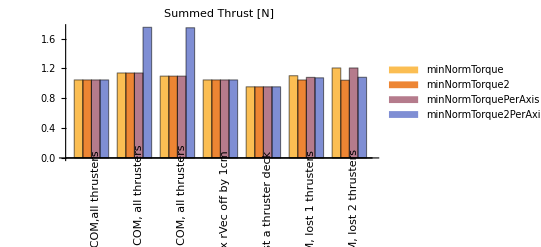

```mathematica
plotBarChart[thrustRMS,"Summed Thrust [N]"]
```

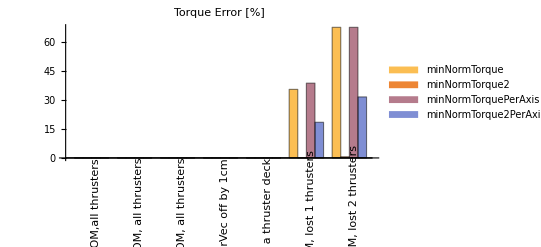

```mathematica
plotBarChart[torqueErrorList,"Torque Error [%]"]
```

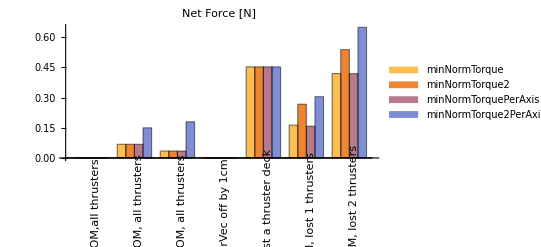

```mathematica
plotBarChart[forceErrorList,"Net Force [N]"]
```

## Performance Comparison with 6 DV Thrusters

## Setup

```mathematica
setup6DVThrusters
```

```mathematica
numThrusters = Length[rVec];
```

```mathematica
Nsamples = 20;
listLr = Table[{RandomReal[]-0.5,RandomReal[]-0.5,RandomReal[]-0.5},{i,Nsamples}];
```

```mathematica
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis,thrusterPairs,optForceTorque, optRMSForceTorque};
functionCalls = {minNormTorque2,optForceTorque};
functionNames = {};
Do[
AppendTo[functionNames,ToString[functionCalls[[i]]]];
,{i,Length[functionCalls]}];
```

```mathematica
minNormTorque2[rVec,gtVec,Lr,B,True]
```

F2(0):{0.807103,-0.994391,-1.80149,-0.807103,0.994391,1.80149}

F(2):{0.807103,-0.994391,-1.80149,-0.807103,0.994391,1.80149}

Rank:2

T.F2:{1.,2.,0.}

Dbar Length:3

Dbar Rank: 2

F2(2):{-1.98878,-3.60299,-1.61421}

F:{0,-1.98878,-3.60299,-1.61421,0,0}

Torque:{1.,2.,0.}

{7.20598,0,-7.20598}

## Comparison

```mathematica
forceErrorList = {};
torqueErrorList = {};
thrustRMS = {};
caseNames={};

AppendTo[caseNames,"DV alignment, 0% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
COM =  Mean[rVec]*1.;
B = {{1,0,0},{0,1,0}};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"DV alignment, 2% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
COM =  Mean[rVec] + {.02, .02,0};
B = {{1,0,0},{0,1,0}};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"DV alignment, 0% COM, lost 2 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
COM =  Mean[rVec];
B = {{1,0,0},{0,1,0}};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVecRed,gtVecRed,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];
```

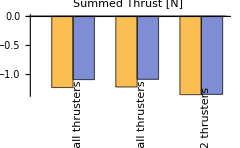

```mathematica
plotBarChart[thrustRMS,"Summed Thrust [N]"]
```

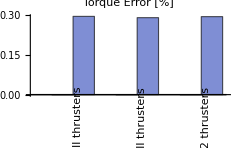

```mathematica
plotBarChart[torqueErrorList,"Torque Error [%]"]
```

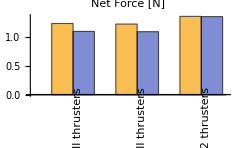

```mathematica
plotBarChart[forceErrorList,"Net Force [N]"]
```

## Performance Comparison with 8 RCS Thrusters (old configuration)

## Setup

```mathematica
setup8ThrustersOldConfig
```

```mathematica
numThrusters = Length[rVec];
```

```mathematica
Nsamples = 20;
listLr = Table[{RandomReal[]-0.5,RandomReal[]-0.5,RandomReal[]-0.5},{i,Nsamples}];
```

```mathematica
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis,thrusterPairs,optForceTorque, optRMSForceTorque};
functionCalls = {minNormTorque,minNormTorque2,optForceTorque};
functionNames = {};
Do[
AppendTo[functionNames,ToString[functionCalls[[i]]]];
,{i,Length[functionCalls]}];
```

```mathematica
functionCalls[[2]][rVec,gtVec,Lr,B,False]
```

{0,0,9.42809}

## Comparison

```mathematica
forceErrorList = {};
torqueErrorList = {};
thrustRMS = {};
caseNames={};

AppendTo[caseNames,"Perfect COM,all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10cm COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec]+{0,0,0.1};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"5% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec]+{0,0,0.05};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, 1x rVec off by 1cm"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = gtVec;
rVec2 = rVec;
rVec2[[1]]+= {0,0.01,0};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10% COM, lost a thruster deck"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec]+{0,0,0.1};
gtVec2 = gtVecRed;
rVec2 = rVecRed;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 1 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 2 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-2];
rVec2 = Drop[rVec,-2];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

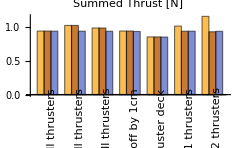

```mathematica
plotBarChart[thrustRMS,"Summed Thrust [N]"]
```

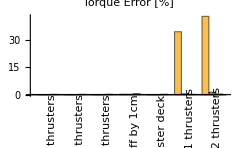

```mathematica
plotBarChart[torqueErrorList,"Torque Error [%]"]
```

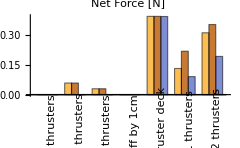

```mathematica
plotBarChart[forceErrorList,"Net Force [N]"]
```

## Performance Comparison with 12 RCS Thrusters

## Setup

```mathematica
setup12Thrusters
```

```mathematica
numThrusters = Length[rVec];
```

```mathematica
Nsamples = 20;
listLr = Table[{RandomReal[]-0.5,RandomReal[]-0.5,RandomReal[]-0.5},{i,Nsamples}];
```

```mathematica
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis,thrusterPairs,optForceTorque, optRMSForceTorque};
functionCalls = {minNormTorque,minNormTorque2,minNormTorquePerAxis,minNormTorque2PerAxis};
functionNames = {};
Do[
AppendTo[functionNames,ToString[functionCalls[[i]]]];
,{i,Length[functionCalls]}];
```

```mathematica
functionCalls[[2]][rVec,gtVec,Lr,B,False]
```

{0,0,9}

## Comparison

```mathematica
forceErrorList = {};
torqueErrorList = {};
thrustRMS = {};
caseNames={};

AppendTo[caseNames,"Perfect COM,all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec]*1.1;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"5% COM, all thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM = Mean[rVec]*1.05;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec,gtVec,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, 1x rVec off by 1cm"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = gtVec;
rVec2 = rVec;
rVec2[[1]]+= {0,0.01,0};
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"10% COM, lost a thruster deck"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec]*1.1;
gtVec2 = gtVecRed;
rVec2 = rVecRed;
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 1 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-1];
rVec2 = Drop[rVec,-1];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];

AppendTo[caseNames,"0% COM, lost 2 thrusters"];
AppendTo[forceErrorList,{}];
AppendTo[torqueErrorList,{}];
AppendTo[thrustRMS,{}];
B = IdentityMatrix[3];
Lr = {1,2,3};
COM =  Mean[rVec];
gtVec2 = Drop[gtVec,-2];
rVec2 = Drop[rVec,-2];
c = Length[forceErrorList];
Do[
ans=Mean[Table[
functionCalls[[i]][rVec2,gtVec2,listLr[[k]],B,False]
,{k,Nsamples}]];
AppendTo[forceErrorList[[c]], ans[[1]]];
AppendTo[torqueErrorList[[c]], ans[[2]]];
AppendTo[thrustRMS[[c]], ans[[3]]];
,{i,Length[functionNames]}];
```

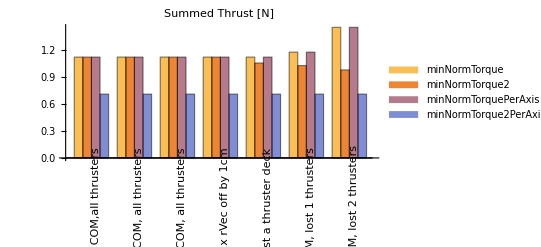

```mathematica
plotBarChart[thrustRMS,"Summed Thrust [N]"]
```

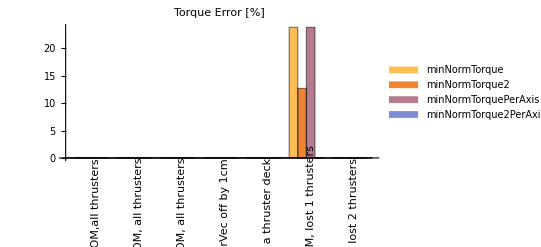

```mathematica
plotBarChart[torqueErrorList,"Torque Error [%]"]
```

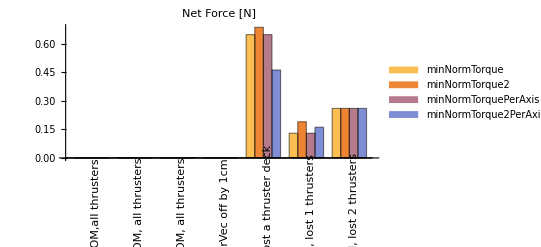

```mathematica
plotBarChart[forceErrorList,"Net Force [N]"]
```

## Old Code

## Using full Optimization on 8 Forces

```mathematica
F3 = {F21,F22,F23,F24,F25,F26,F27,F28};
```

```mathematica
cost[Lr_,B_,FF_]:=Block[{error,ans},

T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];

error=T.FF - Transpose[B].B.Lr ;

Return[error.error];
]
```

```mathematica
ans2=NMinimize[{cost[Lr,B,F3],F3≥0},F3]
```

{7.41513×10^-17,{F21→1.01815,F22→0.8877,F23→1.71262,F24→0.760755,F25→0.546273,F26→0.246406,F27→2.8018,F28→1.05752}}

```mathematica
Fmin = Min[F3 /. ans2[[2]]]
```

0.246406

```mathematica
(F3 /. ans2[[2]] )-Fmin
```

{0.771745,0.641294,1.46622,0.514349,0.299866,0.,2.55539,0.811109}

```mathematica
T.((F3 /. ans2[[2]]) - Fmin)
```

{1.,2.,3.}

```mathematica
F3.F3 /. ans2[[2]]
```

14.664

```mathematica
ans2=NMinimize[{F3.F3,cost[Lr,B,F3]==0,F3≥0},F3,AccuracyGoal->6,MaxIterations->200]
```

{5.35809,{F21→0.566195,F22→1.06765×10^-8,F23→0.495518,F24→0.968147,F25→0.,F26→0.,F27→1.60434,F28→1.13171}}

```mathematica
FFs =Chop[( F3/.ans2[[2]])]
```

{0.566195,1.06765×10^-8,0.495518,0.968147,0,0,1.60434,1.13171}

```mathematica
Transpose[gtVec].FFs
```

{1.27238,-0.566195,0.}

```mathematica
T.FFs
```

{0.999504,1.99999,2.99947}

```mathematica
ans2=NMinimize[{Norm[Transpose[gtVec].F3],cost[Lr,B,F3]==0,F3≥0},F3]
```

{3.10382×10^-10,{F21→0.88535,F22→0.0111913,F23→1.22919,F24→1.48427,F25→0.220854,F26→0.675687,F27→2.55817,F28→0.155294}}

```mathematica
Fmin = Min[F3 /. ans2[[2]]]
```

0.0111913

```mathematica
FFs =( F3/.ans2[[2]]) - Fmin
```

{0.874159,0.,1.218,1.47308,0.209663,0.664496,2.54698,0.144103}

```mathematica
Transpose[gtVec].((F3/.ans2[[2]])-Fmin)
```

{1.75233×10^-10,2.56185×10^-10,0.}

```mathematica
T.FFs
```

{1.,1.99997,2.99973}

## Using full Optimization on 4 Forces

```mathematica
Fred = {F11,F12,F13,F14};
```

```mathematica
cost2[Lr_,B_,FF_]:=Block[{Ffull,error,ans},
Do[
T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];
b = B[[j]];

Ffull = {FF[[1]],FF[[2]], FF[[3]], FF[[4]], FF[[2]], FF[[1]],FF[[4]], FF[[3]]};
error=T.Ffull - Transpose[B].B.Lr;
(*error=T.Ffull - Lr ;*)

ans = error.error;
,{j,Length[B]}];
Return[ans];
]
```

```mathematica
Lr={1,2,3};
COM ={0,0,0};
B = {{1,0,0}};
B = IdentityMatrix[3];
```

### Optimize Torque Error with F>0 Constraint applied afterwards

```mathematica
T = {};
Do[
AppendTo[T,Cross[rVec[[i]]-COM,gtVec[[i]]]];
,{i,Length[rVec]}];
T = Transpose[T];
Tt=Transpose[T];
Tred={
Tt[[1]]+Tt[[6]],
Tt[[2]]+Tt[[5]],
Tt[[3]]+Tt[[8]],
Tt[[4]]+Tt[[7]]
};
Tred = Transpose[Tred];
```

```mathematica
MatrixForm[T]
```

(1.7653 | 0.2604 | 0. | 0. | -1.7653 | -0.2604 | 0. | 0.
0. | 0. | -1.7653 | -0.2604 | 0. | 0. | 1.7653 | 0.2604
-0.8255 | -0.8255 | 0.8255 | 0.8255 | -0.8255 | -0.8255 | 0.8255 | 0.8255)

```mathematica
Lr={1,0,0}
```

{1,0,0}

```mathematica
Fs1=PseudoInverse[Tred].Lr
```

{-0.122022,-0.786518,-0.210226,1.11877}

```mathematica
Fs1 -= Min[Fs1]
```

{0.664496,0.,0.576292,1.90528}

```mathematica
FFs = {Fs1[[1]],Fs1[[2]],Fs1[[3]],Fs1[[4]],Fs1[[2]],Fs1[[1]],Fs1[[4]],Fs1[[3]]}
```

{0.664496,0.,0.576292,1.90528,0.,0.664496,1.90528,0.576292}

```mathematica
FFs.FFs
```

8.80755

```mathematica
Transpose[gtVec].FFs
```

{0.,0.,0.}

```mathematica
T.FFs
```

{1.,2.,3.}

### Optimize Torque Error with F>0 Constraint directly applied

```mathematica
ans3=NMinimize[{cost2[Lr,B,Fred],Fred≥0},Fred,AccuracyGoal->12,MaxIterations->200]
```

{9.16329×10^-22,{F11→0.843167,F12→0.178671,F13→0.754964,F14→2.08396}}

```mathematica
FFs = Chop[{F11,F12,F13,F14,F12,F11,F14,F13}/.ans3[[2]]];
FFs = FFs - Min[FFs]
```

{0.664496,0.,0.576292,1.90528,0.,0.664496,1.90528,0.576292}

```mathematica
Transpose[gtVec].FFs
```

{2.22045×10^-16,0.,0.}

```mathematica
T.FFs
```

{1.,2.,3.}

### Minimize thrust vector magnitude subject to matching torques

```mathematica
ans3=NMinimize[{Fred.Fred,cost2[Lr,B,Fred]==0,Fred≥0},Fred,AccuracyGoal->12,MaxIterations->200]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

{4.40158,{F11→0.664095,F12→0.,F13→0.576009,F14→1.90493}}

```mathematica
FFs = Chop[{F11,F12,F13,F14,F12,F11,F14,F13}/.ans3[[2]]]
```

{0.664095,0,0.576009,1.90493,0,0.664095,1.90493,0.576009}

```mathematica
Transpose[gtVec].FFs
```

{-1.11022×10^-16,0.,0.}

```mathematica
T.FFs
```

{0.999396,1.9999,2.99962}

# Basilisk Unit Tests

## 8 RCS Thruster Setup (BSK)

```mathematica
setup8ThrustersBSK:=Block[{},
rVec = {
{-0.86360,-0.82550,1.79070},
{-0.82550,-0.86360,1.79070},
{0.82550,0.86360,1.79070},
{0.86360,0.82550,1.79070},
{-0.86360,-0.82550,-1.79070},
{-0.82550,-0.86360,-1.79070},
{0.82550,0.86360,-1.79070},
{0.86360,0.82550,-1.79070}
};
COM=Chop[Mean[rVec]];
gtVec = {
{1.0,0.0,0.0},
{0.0,1.0,0.0},
{0.0,-1.0,0.0},
{-1.0,0.0,0.0},
{1.0,0.0,0.0},
{0.0,1.0,0.0},
{0.0,-1.0,0.0},
{-1.0,0.0,0.0}
};
gtVecRed = Drop[gtVec,{1,4}];
rVecRed = Drop[rVec,{1,4}];

numThrusters=Length[rVec];
posThrustFlag =+1;
B = IdentityMatrix[3];
]

setup8ThrustersBSK
```

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVec[[i]],rVec[[i]]+.5gtVec[[i]]}]}
,{Black,PointSize[Large],Point[rVec[[i]]]}
}]
,{i,Length[rVec]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
Show[
Table[
Graphics3D[{
{Blue,Arrowheads[0.05],Arrow[{rVecRed[[i]],rVecRed[[i]]+.5gtVecRed[[i]]}]}
,{Black,PointSize[Large],Point[rVecRed[[i]]]}
}]
,{i,Length[rVecRed]}]
,Boxed->False
,Axes->True
,AxesOrigin->{0,0,0}
,SphericalRegion->True
]
```

-Graphics3D-

```mathematica
setup8ThrustersBSK;
```

```mathematica
Lr = {1,-.5,.7};
```

```mathematica
(* ideal *)
```

```mathematica
minNormTorque2[rVec,gtVec,Lr,B,True]
```

F2(0):{0.0361913,-0.245607,0.0336138,0.175801,0.175801,0.0336138,-0.245607,0.0361913}

F(2):{0.281798,0,0.27922,0.421408,0.421408,0.27922,0,0.281798}

Rank:3

T.F2:{1.,-0.5,0.7}

F:{0.281798,0.,0.27922,0.421408,0.421408,0.27922,0.,0.281798}

Torque:{1.,-0.5,0.7}

{0,0,1.96485}

```mathematica
(* thruster saturation *)
```

```mathematica
ans={0.2817978358269864,0.,0.27922041659686153,0.4214080441254172,0.4214080441254172,0.27922041659686153,0.,0.2817978358269864};
N[ans*10,10]
ans/Max[ans]*.95
```

{2.81798,0.,2.7922,4.21408,4.21408,2.7922,0.,2.81798}

{0.63527,0.,0.62946,0.95,0.95,0.62946,0.,0.63527}

```mathematica
(* dropAxis)
```

```mathematica
minNormTorque2[rVec,gtVec,Lr,{{1,0,0},{0,0,1}},True]
```

F2(0):{0.105996,-0.245607,0.0336138,0.105996,0.105996,0.0336138,-0.245607,0.105996}

F(2):{0.351603,0,0.27922,0.351603,0.351603,0.27922,0,0.351603}

Rank:3

T.F2:{1.,0.,0.7}

F:{0.351603,0.,0.27922,0.351603,0.351603,0.27922,0.,0.351603}

Torque:{1.,0.,0.7}

{0,0,1.96485}

```mathematica
(* dropThruster *)
```

```mathematica
minNormTorque2[Drop[rVec,-1],Drop[gtVec,-1],Lr,B,True]
```

F2(0):{0.057906,-0.252845,0.0263756,0.168563,0.168563,0.0263756,-0.252845}

F(2):{0.310751,0,0.27922,0.421408,0.421408,0.27922,0}

Rank:3

T.F2:{1.,-0.952769,0.491277}

Dbar Length:5

Dbar Rank: 3

F2(2):{0.563596,0.27922,0.421408,0.421408,0.27922}

F:{0.563596,0,0.27922,0.421408,0.421408,0.27922,0}

Torque:{1.,-0.5,0.7}

{0.563596,0,1.96485}

```mathematica
Table[
{minNormTorque2[Drop[rVec,-1],Drop[gtVec,-1],
ans={Random[]-.5,Random[]-.5,Random[]-.5},B,False],ans}
,{i,10}]
```

{{{0.0887045,0,0.402044},{0.480663,0.158843,-0.185436}},{{0.126387,0,0.651368},{0.251001,0.226321,-0.329039}},{{0.0890631,0,0.425968},{-0.424742,0.159485,-0.204594}},{{0.0140118,5.17149,0.448646},{-0.460337,-0.267782,-0.0424995}},{{0.271476,0,0.818039},{0.475813,-0.0167835,0.236598}},{{0.270506,0,0.438228},{0.2486,0.484396,0.0848485}},{{0.213351,0,0.594974},{0.337673,0.0363497,0.179821}},{{0,0,0.578704},{0.0659727,-0.29421,-0.206463}},{{0.406251,0,0.696363},{0.199159,0.40713,0.391226}},{{0.286948,0,0.333599},{0.0425358,0.472837,0.236168}}}

```mathematica
COM = {0,0,0.02};
```

```mathematica
(* use COM *)
```

```mathematica
minNormTorque2[rVec,gtVec,Lr,B,True]
```

F2(0):{0.0369795,-0.24403,0.0320373,0.175013,0.176572,0.0351555,-0.247148,0.0354204}

F(2):{0.284128,0.00311817,0.279186,0.422161,0.423721,0.282304,0,0.282569}

Rank:3

T.F2:{1.,-0.5,0.7}

F:{0.284128,0.00311817,0.279186,0.422161,0.423721,0.282304,0.,0.282569}

Torque:{1.,-0.5,0.7}

{0.00697245,0,1.97719}

## 6 DV Thruster Setup (BSK)

```mathematica
setup6DVThrusters
```

```mathematica
Lr = {1,-.5,.7};
```

```mathematica
minNormTorque2[rVec,gtVec,Lr,B,True]
```

F2(0):{0.807103,0.753037,-0.0540656,-0.807103,-0.753037,0.0540656}

F(2):{0.807103,0.753037,-0.0540656,-0.807103,-0.753037,0.0540656}

Rank:2

T.F2:{1.,-0.5,0.}

Dbar Length:3

Dbar Rank: 2

F2(2):{-0.108131,-1.61421,-1.50607}

F:{0,0,-0.108131,-1.61421,-1.50607,0}

Torque:{1.,-0.5,0.}

{3.22841,0,-3.22841}

```mathematica
minNormTorque2[rVecRed,gtVecRed,Lr,B,True]
```

F2(0):{1.56014,-0.861168,-1.56014,0.861168}

F(2):{1.56014,-0.861168,-1.56014,0.861168}

Rank:2

T.F2:{1.,-0.5,0.}

Dbar Length:2

Dbar Rank: 2

F2(2):{-1.72234,-3.12028}

F:{0,-1.72234,-3.12028,0}

Torque:{1.,-0.5,0.}

{4.84262,0,-4.84262}

```mathematica
COM = {0,0,0.02};
```

```mathematica
minNormTorque22[rVec,gtVec,Lr,B,True]
```

F2(0):{0.807103,0.753037,-0.0540656,-0.807103,-0.753037,0.0540656}

F(2):{0.807103,0.753037,-0.0540656,-0.807103,-0.753037,0.0540656}

Rank:2

T.F2:{1.,-0.5,0.}

Dbar Length:3

Dbar Rank: 2

F2(2):{-0.108131,-1.61421,-1.50607}

F:{0,0,-0.108131,-1.61421,-1.50607,0}

Torque:{1.,-0.5,0.}

{3.22841,0,-3.22841}

```mathematica
0,0,-0.1081312318123977,-1.6142050040355125,-1.5060737722231148,0
```

```mathematica
0,-1.722336235847909,-3.120278776258626,0
```